Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario C: high water influx, water_in=750

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
kh=0.1;
kw=0.01;
n=0.1;
a=0.5;
```

Define water recharge rates:

```mathematica
win=750;
ws=alpha*(win-beta)

wt= win-ws
```

180.

570.

Define system without fire effects

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→453.333-0.6 W}}

```mathematica
p1=Plot[453.3333333333333-0.6* W,{W,0,750}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,W]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→318.75-0.833333 H-0.416667 √(974025.-900. H+4. H^2)},{W→0.416667 (765.-2. H+√(974025.-900. H+4. H^2))}}

```mathematica
Simplify[Solve[W==318.75-0.8333333333333334*H-0.4166666666666667* √(974025-900* H+4*H^2),H]]
```

{{H→(405000.+3825. W-6. W^2)/(-2250.+10. W)}}

```mathematica
p2=Plot[(405000+3825* W-6* W^2)/(-2250+10* W),{W,0,750},PlotStyle->Red];
```

```mathematica
Simplify[Solve[W==0.4166666666666667* (765-2*H+√(974025-900* H+4* H^2)),H]]
```

{{H→(405000.+3825. W-6. W^2)/(-2250.+10. W)}}

Get the same solution, so we can disregard!

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→-92.4696},{H→37.9487,W→692.308},{H→0.,W→729.97}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→-92.4696}

```mathematica
fp2=Part[fp,2]
```

{H→37.9487,W→692.308}

```mathematica
fp3=Part[fp,3]
```

{H→0.,W→729.97}

```mathematica
p1h=37.94871794871795;
p1w=692.3076923076923;

p2h=0;
p2w=729.9696037398995;
```

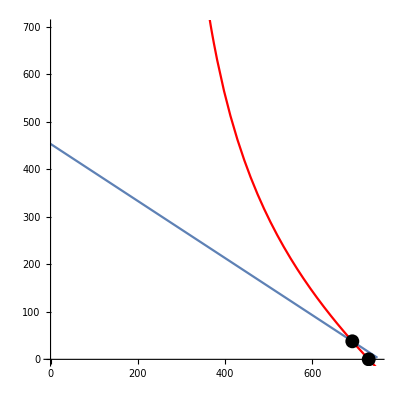

```mathematica
Show[p1,p2,Graphics[{PointSize[0.025],Point[{p1w,p1h}]}],Graphics[{PointSize[0.025],Point[{p2w,p2h}]}],PlotRange->{0,700},AspectRatio->1]
```

Jacobian evaluated at first fixed point: unstable fixed point, non physical

```mathematica
j11=D[dhdt[H,W],H]/.fp1;
j12=D[dhdt[H,W],W]/.fp1;
j21=D[dwdt[H,W],H]/.fp1;
j22=D[dhdt[H,W],W]/.fp1;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{3.67764,0.}

Jacobian evaluated at second fixed point: unstable saddle node

```mathematica
j11=D[dhdt[H,W],H]/.fp2;
j12=D[dhdt[H,W],W]/.fp2;
j21=D[dwdt[H,W],H]/.fp2;
j22=D[dhdt[H,W],W]/.fp2;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{-0.141458,0.0551742}

Jacobian evaluated at third fixed point: unstable fixed point on the boundary (or is it supposed to be 0,0?)

```mathematica
j11=D[dhdt[H,W],H]/.fp3;
j12=D[dhdt[H,W],W]/.fp3;
j21=D[dwdt[H,W],H]/.fp3;
j22=D[dhdt[H,W],W]/.fp3;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{0.0223573,0.}